```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final-CPK-Messing-Around/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->ConsumerGrowth,μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

```mathematica
RSS
```

(μ (-λ+σ))/(2 λ ρ+μ σ)

```mathematica
HSS
```

-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
Fstar
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u->{u,…},c_v->{v,…},…] links the controls to the specified controllers on an external device.

```mathematica
ConsumerGrowth2=ConsumerGrowth/.{M->1000}
Mortality2=Mortality/.{M->1000}
FullMaintenance2=FullMaintenance/.{M->1000}
StarveMaintenance2=StarveMaintenance/.{M->1000}
ResourceGrowth2=ResourceGrowth/.{M->1000}
Starvation2=Starvation/.{M->1000}
Recovery2=Recovery/.{M->1000}
```

5.76974×10^-8

2.23356×10^-6

8.17095×10^-8

1.79783×10^-9

9.45×10^-9

0.0000153044

3.26251×10^-7

```mathematica
Manipulate[ToString[λ]<>ToString[μ],{{λ,ConsumerGrowth2,"λ"},.1*ConsumerGrowth2,10*ConsumerGrowth2},{{μ,Mortality2,"μ"},.1*Mortality2,10*Mortality2}]
```

```mathematica
tstfn=Fstar/.{M->1000}
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
tstfn
```

-(3.02359×10^-26 (-0.0000153044+λ) λ)/((3.41835×10^-11+6.52502×10^-7 λ) (3.41835×10^-11 (1.82503×10^-13+3.28049×10^-7 λ)+3.26251×10^-7 (3.65007×10^-13-2.22997×10^-6 λ) λ))

```mathematica
tstfn/.{λ->ConsumerGrowth2}
```

0.000112808

```mathematica
Fstar
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
Fstar
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
Fstar/.{λ->ConsumerGrowth2,μ->Mortality2,β->FullMaintenance2,δ->StarveMaintenance2,α->ResourceGrowth2,σ->Starvation2,ρ->Recovery2}
```

0.000112808

```mathematica
YH2=YH/.{M->1000}
```

0.00782983

```mathematica
dimF/.{M->1000}
(Fstar*YH2*k)/.{λ->ConsumerGrowth2,μ->Mortality2,β->FullMaintenance2,δ->StarveMaintenance2,α->ResourceGrowth2,σ->Starvation2,ρ->Recovery2}
```

0.045709

0.045709

```mathematica
Manipulate[Show[{
(*ListLogLogPlot[data,PlotRange->{{.001,10^10},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],*)
LogLogPlot[{dimH/M,dimF/M},{M,.001,10^10},PlotStyle->{Red,Blue}](*,
ListLogLogPlot[data]*)
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Red,Dashed,Thickness[.0075]}]],
ListLogLogPlot[{{1000,((-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)))*YH2*k)/1000}},PlotStyle->{Black,PointSize[.01]}]
}]
,
{{σ,Starvation2,"σ"},.1*Starvation2,10*Starvation2},
{{α,ResourceGrowth2,"α"},.1*ResourceGrowth2,4.5*ResourceGrowth2},
{{β,FullMaintenance2,"β"},.1*FullMaintenance2,10*FullMaintenance2},
{{λ,ConsumerGrowth2,"λ"},.1*ConsumerGrowth2,10*ConsumerGrowth2},
{{μ,Mortality2,"μ"},.1*Mortality2,10*Mortality2},
{{ρ,Recovery2,"ρ"},.1*Recovery2,10*Recovery2},
{{δ,StarveMaintenance2,"δ"},.1*StarveMaintenance2,10*StarveMaintenance2}
]
```

```mathematica
4.5*ResourceGrowth2
```

9.45×10^-9

Energy equivalence hypothesis

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv","csv"];
```

```mathematica
Mean[data[[All,2]]]
```

0.000791639

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

Graphics::gprim: ColorData[97, 2] was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: ColorData[97, 3] was encountered where a Graphics primitive or directive was expected.

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

Graphics::gprim: ColorData[97, 3] was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics :: gprim will be suppressed during this calculation.

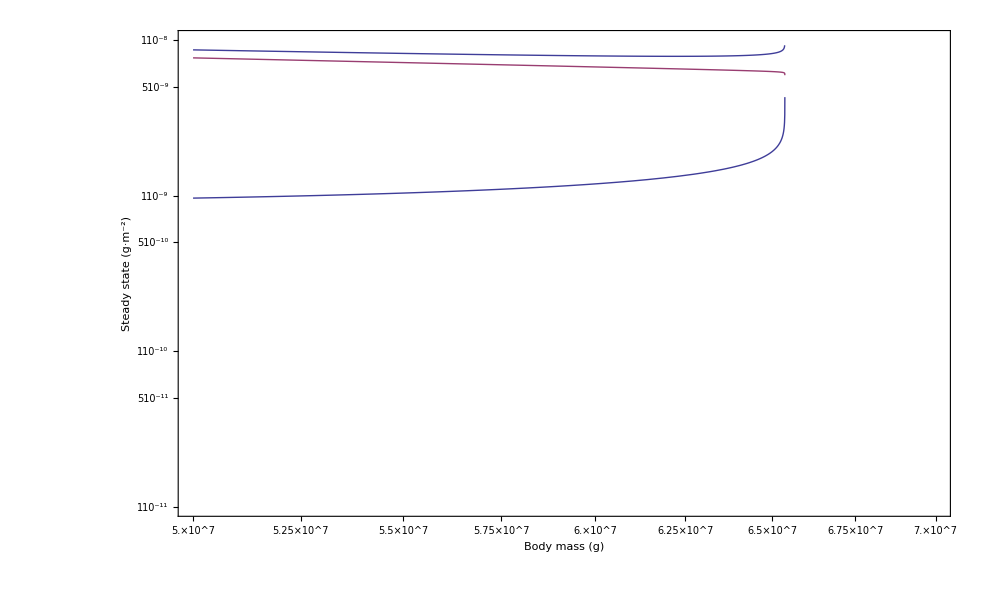

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{5*10^7,7*10^7},{10^-11,10^(-8)}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,5*10^7,7*10^7},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,5*10^7,7*10^7},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
```

```mathematica
B0
```

0.047

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

Graphics::gprim: ColorData[97, 2] was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: ColorData[97, 3] was encountered where a Graphics primitive or directive was expected.

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

Graphics::gprim: ColorData[97, 3] was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics :: gprim will be suppressed during this calculation.

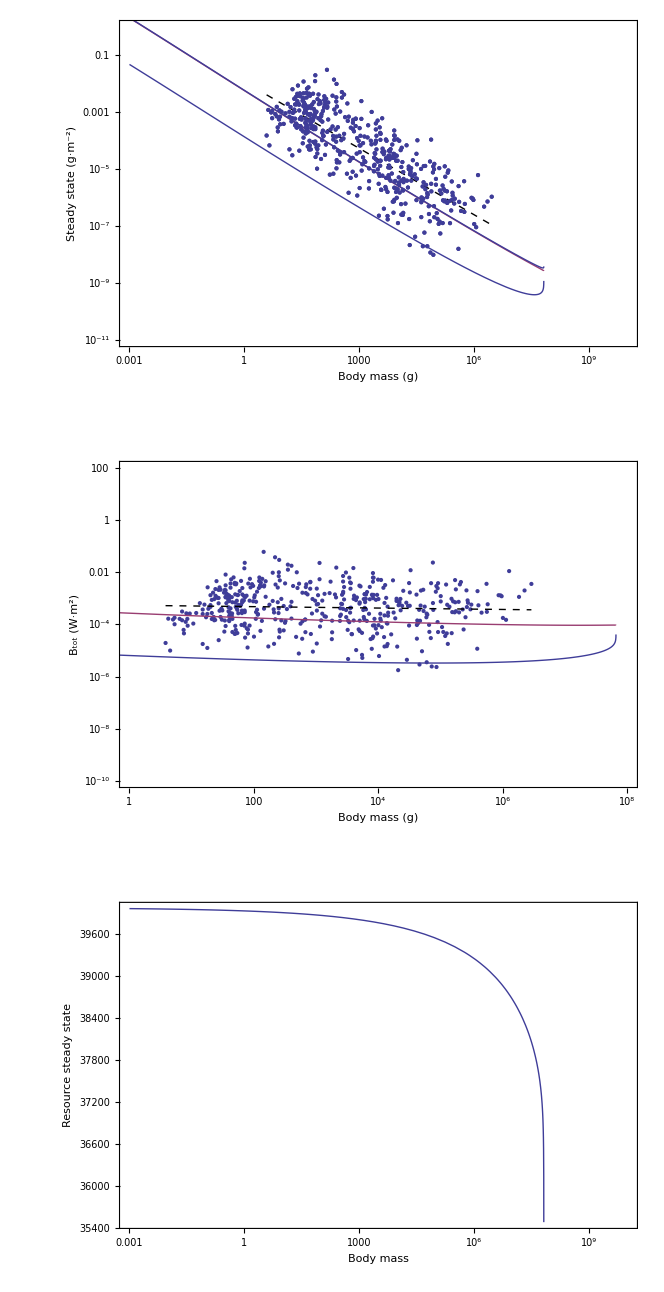

```mathematica
Cplot=GraphicsGrid[{{
Show[{
ListLogLogPlot[data,PlotRange->{{.001,10^10},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,.001,10^10},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,.001,10^10},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
},{
Show[{
ListLogLogPlot[Table[{data[[i]][[1]],data[[i]][[2]]*(data[[i]][[1]])^(3/4)*B0},{i,Length[data]}],PlotRange->{{1,10^8},{10^-10,100}},Frame->True,FrameLabel->{"Body mass (g)","B_tot (W·m^2)"}],
LogLogPlot[0.0115643*M^(-0.776818)*M^(3/4)*B0,{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
LogLogPlot[{dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0},{M,.001,10^10},Frame->True,FrameLabel->{"Body mass (g)","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]}]
},{
LogLinearPlot[dimR,{M,.001,10^10},Frame->True,PlotRange->All,FrameLabel->{"Body mass","Resource steady state"}]
}}]
```

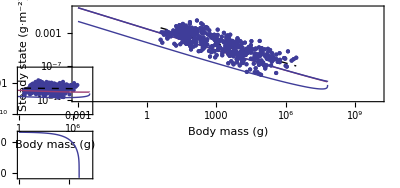

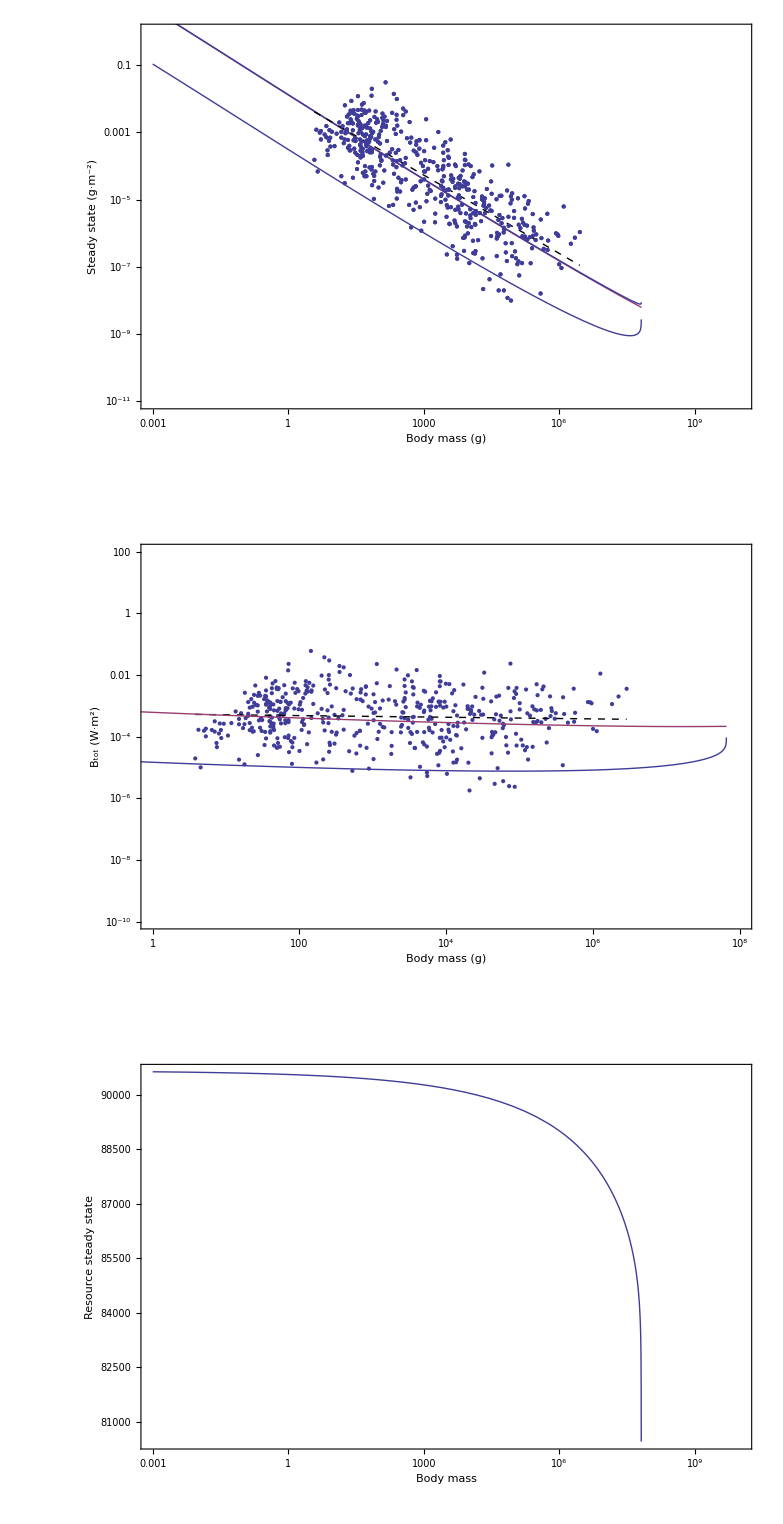

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf"}],Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf

```mathematica
NIntegrate[(1/M)*(dimF/M*M^(3/4)*B0),{M,10^3,10^5}]
```

0.000132489

```mathematica
FindMaximum[Re[HFM[[1]]],M]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.59227,{M→6.53794×10^7}}

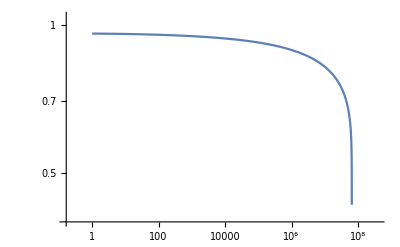

```mathematica
LogLogPlot[StarRates[[1]],{M,1,10^9},PlotRange->All]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}